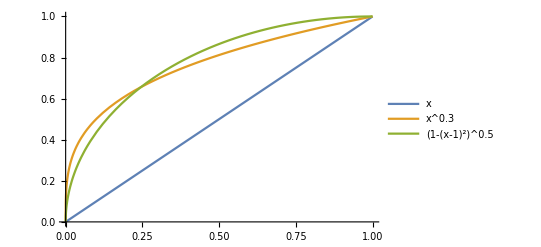

{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}

{-5.,1.53835,4.,5.71214,7.,7.99038,8.74773,9.30909,9.69694,9.92481,10.}

```mathematica
(*
Zeno's Range Selector:
Goal={0,1}->{0,0.5,0.25,...}
*)

Plot[
{x,x^0.3,(1-(x-1)^2)^0.5},{x,0,1},PlotLegends->"Expressions"
]

min=2;
max=4;
sq=(1-(#-1)^2)^0.5&;

(Range[min,max,(max-min)/10.]/(max-min)-1.)/10.
ChopRange[min_,max_,res_,func_]:=func@(Range[0,1,1/res])*(max-min)+min
ChopRange[-5,10,10.,sq]
```